```mathematica
RICOSTRUZIONE 
								DEL MODELLO
		SISMOSTRATIGRAFICO del sottosuolo
		con l'utilizzo della sismica a rifrazione
				

					    Corso di Metodi numerici per la Geologia (A.A. 2014/2015)
                  Laurea Magistrale in Geologia e territorio - Curriculum Rischio idrogeologico


                                                                            Sara Mazzotta,matricola 00000000000
                                                                                                                                                                                        Vera Federica Rizzi,matricola 0000745459


					-Graphics- -Graphics-
```

OBIETTIVO
Lo scopo del progetto è quello di effettuare una corretta interpretazione del sottosuolo, tramite l’utilizzo della tecnica esplorativa nota come sismica a rifrazione , mediante il calcolo dei parametri caratteristici di un terreno , quali velocità di propagazione delle onde P e spessore degli strati.

UBICAZIONE DELLA PROVA SISMICA
La prova si è svolta in data 11/11/2014 presso i giardini Parker-Lennon di Bologna. 

SVOLGIMENTO DELLA PROVA
       ONDE P
       Posizionamento in superficie di uno stendimento sismico lineare di lunghezza 60 m, costituito da 16 geofoni verticali a distanza di 4 m. 
       Per generare le onde P sono stati utilizzati diversi tipi di sorgente (fucile sismico con tiro diretto e inverso, mazza da 5 kg, salto, 
       caduta di un grave da 12 kg).


IMPORTAZIONE E PREPARAZIONE DEI DATI DI ONDE P
I dati che abbiamo importato riguardano la distanza sorgente-ricevitore (in m) e i tempi di arrivo delle onde (in ms) al tiro diretto e inverso.
Abbiamo generato due liste (formato .txt), a cui abbiamo assegnato il nome “datiPtirodiretto” e “datiPtiroinverso”, di seguito riportati:

```mathematica
datiPtirodiretto=Import["C:\\p-tirodiretto.txt","Table","DateStringFormat"->{"distanza sorgente-ricevitore","tempi d'arrivo"}]
```

{{0,0},{6,29.2},{10,39.2},{14,58.5},{18,66.4},{22,76.1},{26,85.9},{30,93.7},{34,95.7},{38,101.5},{42,109.3},{44,115.2},{48,115.2},{53,125},{56,123},{60,125}}

```mathematica
datiPtiroinverso=Import["C:\\p-tiroinverso.txt","Table","DateStringFormat"->{"distanza sorgente-ricevitore","tempi d'arrivo"}]
```

{{2,123},{6,119.3},{10,111.3},{14,105.4},{18,101.5},{22,97.6},{26,89.8},{30,85.9},{34,82},{38,76.1},{42,66.4},{44,60.5},{48,44.9},{53,33.2},{56,19.5},{60,0}}

Per favorire la visualizzazione dei dati, sistemiamoli in tabelle usando il comando “TableForm”:

```mathematica
TableForm[datiPtirodiretto,TableHeadings->{None,{"distanza sorgente-ricevitore(m)","tempi d'arrivo(ms)"}}]
```

distanza sorgente-ricevitore(m) | tempi d'arrivo(ms)
0 | 0
6 | 29.2
10 | 39.2
14 | 58.5
18 | 66.4
22 | 76.1
26 | 85.9
30 | 93.7
34 | 95.7
38 | 101.5
42 | 109.3
44 | 115.2
48 | 115.2
53 | 125
56 | 123
60 | 125

```mathematica
TableForm[datiPtiroinverso,TableHeadings->{None,{"distanza sorgente-ricevitore(m)","tempi d'arrivo(ms)"}}]
```

distanza sorgente-ricevitore(m) | tempi d'arrivo(ms)
2 | 123
6 | 119.3
10 | 111.3
14 | 105.4
18 | 101.5
22 | 97.6
26 | 89.8
30 | 85.9
34 | 82
38 | 76.1
42 | 66.4
44 | 60.5
48 | 44.9
53 | 33.2
56 | 19.5
60 | 0

Per visualizzare la coppia di coordinate relativa ad ogni punto, usiamo il comando “Take”:

```mathematica
coordinate=Take[datiPtirodiretto,All]
```

{{0,0},{6,29.2},{10,39.2},{14,58.5},{18,66.4},{22,76.1},{26,85.9},{30,93.7},{34,95.7},{38,101.5},{42,109.3},{44,115.2},{48,115.2},{53,125},{56,123},{60,125}}

```mathematica
coordinate2=Take[datiPtiroinverso,All]
```

{{2,123},{6,119.3},{10,111.3},{14,105.4},{18,101.5},{22,97.6},{26,89.8},{30,85.9},{34,82},{38,76.1},{42,66.4},{44,60.5},{48,44.9},{53,33.2},{56,19.5},{60,0}}

Plottiamo i dati del tiroDiretto e del tiroInverso sul grafico distanzaSR-tempo, usando il comando “ListPlot” ; in seguito, con il comando “Show” uniamo le due liste di dati per avere una visione dell’insieme.

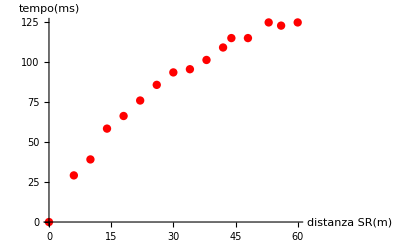

```mathematica
graficopunti1=ListPlot[coordinate,PlotStyle->{Red,PointSize[0.015]},AxesLabel-> {distanza SR[m],tempo[ms]},AxesOrigin-> {0,0}]
```

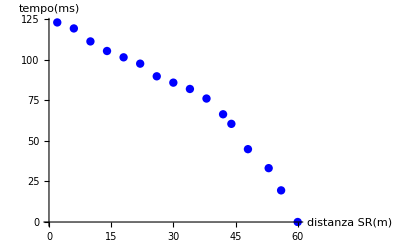

```mathematica
graficopunti2=ListPlot[coordinate2,PlotStyle->{Blue,PointSize[0.015]},AxesLabel-> {distanza SR[m],tempo[ms]},AxesOrigin-> {0,0}]
```

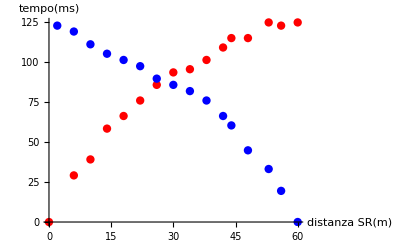

```mathematica
Show[graficopunti1,graficopunti2]
```

In seguito, creiamo una “Module” al fine di plottare le coordinate dei nostri valori sul grafico distanzaSR-tempo, relativa al tiro diretto e inverso; questo grafico permetterà una prima visualizzazione dell’andamento dei punti  nello spazio e nel tempo:

```mathematica
plotDiretto[coordinate_,graficopunti1_]:=
Module[{listadati,grafico},
listadati=graficopunti1[[1]];
grafico=Take[coordinate,listadati];
ListPlot[graficopunti1,grafico,2]]
```

```mathematica
plotInverso[coordinate2_,graficopunti2_]:=
Module[{listadati2,grafico2},
listadati2=graficopunti2 [[1]];
grafico2=Take[coordinate2,listadati2];
ListPlot[graficopunti2,grafico2,2]]
```

Segue un’interpretazione più accurata delle rette di regressione che meglio interpolano i punti; l’analisi è stata effettuata distinguendo i dati in diversi intervalli:

```mathematica
tempo1aPDiretto={0,29.2,39.2,58.5}
```

{0,29.2,39.2,58.5}

```mathematica
dimensione1a=Length[tempo1aPDiretto]
```

4

```mathematica
distanza1aSRPdiretto={0,6,10,14}
```

{0,6,10,14}

```mathematica
coordinate1aPtirodiretto=Table[{Part[distanza1aSRPdiretto,i],Part[tempo1aPDiretto,i]},{i,1,dimensione1a}];TableForm[coordinate1aPtirodiretto]
```

0 | 0
6 | 29.2
10 | 39.2
14 | 58.5

```mathematica
dromocronaregressione1aPdiretta=Fit[coordinate1aPtirodiretto,{1,x},x]
```

1.2729+4.06028 x

```mathematica
punti1aPtirodiretto=ListPlot[coordinate1aPtirodiretto,PlotStyle->{Red,PointSize[0.015]},AxesLabel-> {distanza SR[m],tempo[ms]},AxesOrigin->{0,0}];
```

```mathematica
dromocrona1aPdiretta=Plot[dromocronaregressione1aPdiretta,{x,0,14},PlotStyle->Red];
```

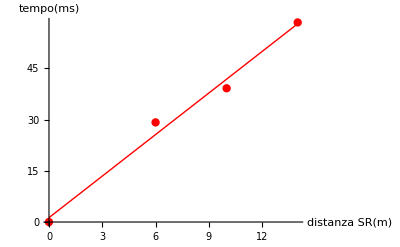

```mathematica
Show[punti1aPtirodiretto,dromocrona1aPdiretta]
```

```mathematica
tempo1bPDiretto={58.5,66.4,76.1,85.9,93.7}
```

{58.5,66.4,76.1,85.9,93.7}

```mathematica
dimensione1b=Length[tempo1bPDiretto]
```

5

```mathematica
distanza1bSRPdiretto={14,18,22,26,30}
```

{14,18,22,26,30}

```mathematica
coordinate1bPtirodiretto=Table[{Part[distanza1bSRPdiretto,i],Part[tempo1bPDiretto,i]},{i,1,dimensione1b}];TableForm[coordinate1bPtirodiretto]
```

14 | 58.5
18 | 66.4
22 | 76.1
26 | 85.9
30 | 93.7

```mathematica
dromocronaregressione1bPdiretta=Fit[coordinate1bPtirodiretto,{1,x},x]
```

26.675+2.2475 x

```mathematica
punti1bPtirodiretto=ListPlot[coordinate1bPtirodiretto,PlotStyle->{Red,PointSize[0.015]},AxesLabel-> {distanza SR[m],tempo[ms]},AxesOrigin->{14,58.5}];
```

```mathematica
dromocrona1bPdiretta=Plot[dromocronaregressione1bPdiretta,{x,14,30},PlotStyle->Red];
```

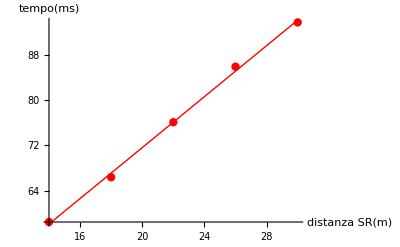

```mathematica
Show[punti1bPtirodiretto,dromocrona1bPdiretta]
```

```mathematica
tempo1cPDiretto={93.7,95.7,101.5,109.3,115.2,115.2,125,123,125}
```

{93.7,95.7,101.5,109.3,115.2,115.2,125,123,125}

```mathematica
dimensione1c=Length[tempo1cPDiretto]
```

9

```mathematica
distanza1cSRPdiretto={30,34,38,42,44,48,53,56,60}
```

{30,34,38,42,44,48,53,56,60}

```mathematica
coordinate1cPtirodiretto=Table[{Part[distanza1cSRPdiretto,i],Part[tempo1cPDiretto,i]},{i,1,dimensione1c}];TableForm[coordinate1cPtirodiretto]
```

30 | 93.7
34 | 95.7
38 | 101.5
42 | 109.3
44 | 115.2
48 | 115.2
53 | 125
56 | 123
60 | 125

```mathematica
dromocronaregressione1cPdiretta=Fit[coordinate1cPtirodiretto,{1,x},x]
```

58.9856+1.16723 x

```mathematica
punti1cPtirodiretto=ListPlot[coordinate1cPtirodiretto,PlotStyle->{Red,PointSize[0.015]},AxesLabel-> {distanza SR[m],tempo[ms]},AxesOrigin->{30,93.7}];
```

```mathematica
dromocrona1cPdiretta=Plot[dromocronaregressione1cPdiretta,{x,30,60},PlotStyle->Red];
```

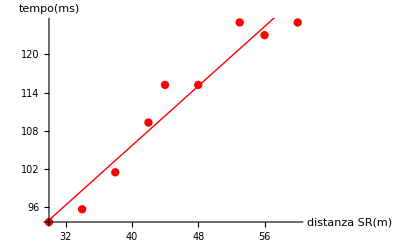

```mathematica
Show[punti1cPtirodiretto,dromocrona1cPdiretta]
```

Ecco ricostruito l’andamento complessivo della dromocrona degli arrivi diretti:

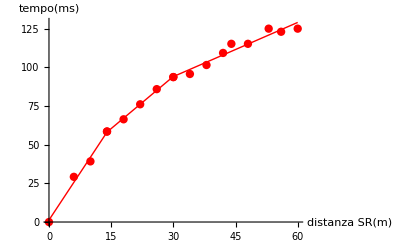

```mathematica
Show[{punti1aPtirodiretto,dromocrona1aPdiretta},{punti1bPtirodiretto,dromocrona1bPdiretta},{punti1cPtirodiretto,dromocrona1cPdiretta},AxesLabel-> {distanza SR[m],tempo[ms]}, PlotRange->All]
```

Facciamo lo stesso procedimento per gli arrivi inversi, suddivisi in intervalli:

```mathematica
tempo1aPInverso={44.9,33.2,19.5,0}
```

{44.9,33.2,19.5,0}

```mathematica
dimensione2a=Length[tempo1aPInverso]
```

4

```mathematica
distanza1aSRPInverso={48,53,56,60}
```

{48,53,56,60}

```mathematica
coordinate1aPtiroInverso=Table[{Part[distanza1aSRPInverso,i],Part[tempo1aPInverso,i]},{i,1,dimensione2a}];TableForm[coordinate1aPtiroInverso]
```

48 | 44.9
53 | 33.2
56 | 19.5
60 | 0

```mathematica
dromocronaregressione1aPInversa=Fit[coordinate1aPtiroInverso,{1,x},x]
```

227.97-3.75244 x

```mathematica
punti1aPtiroInverso=ListPlot[coordinate1aPtiroInverso,PlotStyle->{Blue,PointSize[0.015]},AxesLabel-> {distanza SR[m],tempo[ms]},AxesOrigin->{60,0}];
```

```mathematica
dromocrona1aPinversa=Plot[dromocronaregressione1aPInversa,{x,48,60},PlotStyle->Blue];
```

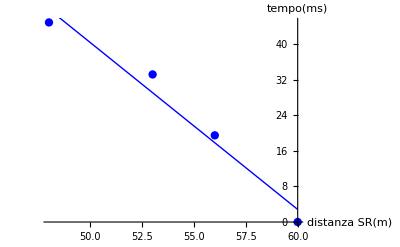

```mathematica
Show[punti1aPtiroInverso,dromocrona1aPinversa]
```

```mathematica
tempo1bPInverso={76.1,66.4,60.5,44.9}
```

{76.1,66.4,60.5,44.9}

```mathematica
dimensione2a=Length[tempo1bPInverso]
```

4

```mathematica
distanza1bSRPInverso={38,42,44,48}
```

{38,42,44,48}

```mathematica
coordinate1bPtiroInverso=Table[{Part[distanza1bSRPInverso,i],Part[tempo1bPInverso,i]},{i,1,dimensione2a}];TableForm[coordinate1bPtiroInverso]
```

38 | 76.1
42 | 66.4
44 | 60.5
48 | 44.9

```mathematica
dromocronaregressione1bPInversa=Fit[coordinate1bPtiroInverso,{1,x},x]
```

195.854-3.11346 x

```mathematica
punti1bPtiroInverso=ListPlot[coordinate1bPtiroInverso,PlotStyle->{Blue,PointSize[0.015]},AxesLabel-> {distanza SR[m],tempo[ms]},AxesOrigin->{48,44.9}];
```

```mathematica
dromocrona1bPinversa=Plot[dromocronaregressione1bPInversa,{x,38,48},PlotStyle->Blue];
```

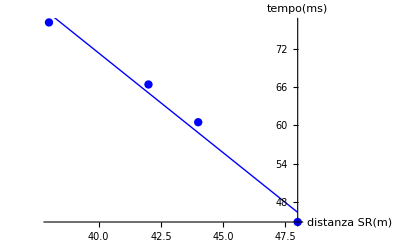

```mathematica
Show[punti1bPtiroInverso,dromocrona1bPinversa]
```

```mathematica
tempo1cPInverso={123,119.3,111.3,105.3,101.5,97.6,89.8,85.9,82,76.1}
```

{123,119.3,111.3,105.3,101.5,97.6,89.8,85.9,82,76.1}

```mathematica
dimensione2a=Length[tempo1cPInverso]
```

10

```mathematica
distanza1cSRPInverso={2,6,10,14,18,22,26,30,34,38}
```

{2,6,10,14,18,22,26,30,34,38}

```mathematica
coordinate1cPtiroInverso=Table[{Part[distanza1cSRPInverso,i],Part[tempo1cPInverso,i]},{i,1,dimensione2a}];TableForm[coordinate1cPtiroInverso]
```

2 | 123
6 | 119.3
10 | 111.3
14 | 105.3
18 | 101.5
22 | 97.6
26 | 89.8
30 | 85.9
34 | 82
38 | 76.1

```mathematica
dromocronaregressione1cPInversa=Fit[coordinate1cPtiroInverso,{1,x},x]
```

125.259-1.30394 x

```mathematica
punti1cPtiroInverso=ListPlot[coordinate1cPtiroInverso,PlotStyle->{Blue,PointSize[0.015]},AxesLabel-> {distanza SR[m],tempo[ms]},AxesOrigin->{38,76.1}];
```

```mathematica
dromocrona1cPinversa=Plot[dromocronaregressione1cPInversa,{x,2,38},PlotStyle->Blue];
```

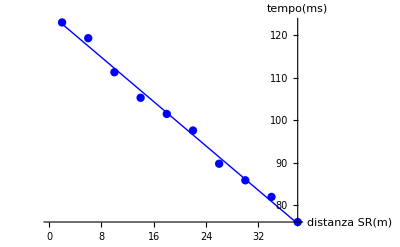

```mathematica
Show[punti1cPtiroInverso,dromocrona1cPinversa]
```

Ecco ricostruito l’andamento complessivo della dromocrona degli arrivi inversi:

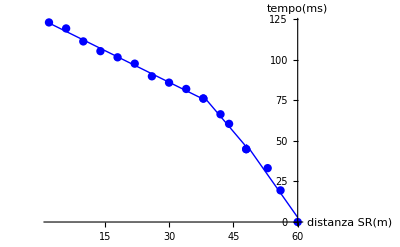

```mathematica
Show[{punti1aPtiroInverso,dromocrona1aPinversa},{punti1bPtiroInverso,dromocrona1bPinversa},{punti1cPtiroInverso,dromocrona1cPinversa},AxesLabel-> {distanza SR[m],tempo[ms]},PlotRange->All]
```

```mathematica
plotDiretto=Show[{punti1aPtirodiretto,dromocrona1aPdiretta},{punti1bPtirodiretto,dromocrona1bPdiretta},{punti1cPtirodiretto,dromocrona1cPdiretta},AxesLabel-> {distanza SR[m],tempo[ms]},PlotRange->All]
```

-Graphics-

```mathematica
plotInverso=Show[{punti1aPtiroInverso,dromocrona1aPinversa},{punti1bPtiroInverso,dromocrona1bPinversa},{punti1cPtiroInverso,dromocrona1cPinversa},AxesLabel-> {distanza SR[m],tempo[ms]},PlotRange->All]
```

-Graphics-

Segue il grafico finale, ottenuto con il comando”Show”, che permette una visualizzazione finale e complessiva del problema in esame:

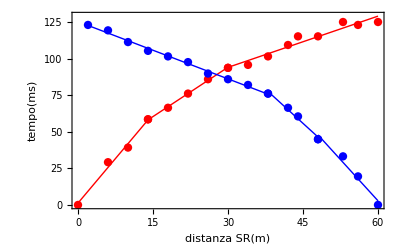

```mathematica
Show[plotDiretto,plotInverso,Frame->True,FrameLabel->{distanza SR[m],tempo[ms]}]
```

Grazie al grafico finale sovrastante, relativo ai tiri diretti ed inversi in relazione alla distanza sorgente-ricevitore sull’asse delle ascisse e tempo sull’asse delle ordinate,  possiamo calcolare velocità e spessore degli strati e ottenere il modello del sottosuolo dell’area studiata:
- la velocità è l’inverso della pendenza: 
 V1= Δx/Δy = 14/60 = 0.233 X1000 = 233 m/s
 V2= 460 m/s
 V3= 860 m/s
 - lo spessore si determina tracciando la linea intercetta dal primo segmento di dromocrona, tramite il metodo del tempo intercetto:
 t0 = 25 ms = 25*10^-3 s
 h1= (t0(v2 * v1))/(2 √(v2^2-v1^2)) = (25(460*233))/(2 √(211600-54289)) = 2679.5/793.24 ≃ 4 m 
 t1 = 55 * 10^-3 s 
 h2 = 15 m

Ecco riassunto il modello sismostratigrafico del terreno oggetto di studio, dal quale si deduce un sistema a tre strati pianoparalleli. 
In relazione alle diverse velocità delle onde P, si possono ipotizzare diverse litologie, a testimonianza di materiali a diversa competenza e compattazione (che generalmente aumenta con la profondità): i primi metri sono costituiti da terreni argillosi, come si evince dalle basse velocità delle onde P, mentre in profondità si assiste ad un notevole aumento delle Vp e ciò indica un cambio litologico verso granuometrie più grossolane;si potrebbe trattare di terreno ghiaioso.

```mathematica
modellosismostratigrafico=Import["C:\\tabella.JPG"]
```

-Graphics-